## Visualizing Stochastic Loewner Evolution (SLE) through the zipper algorithm

The function gm maps the upper half plane to the upper half plane minus a slit of size approximately 1/m at an angle απ from the positive x-axis.  When we repeatedly iterate this map, randomizing the angle at each step, we obtain a visualization of SLE.  

The following code gives us some building blocks for this simulation.  “ListIteratesFixedBase” and “ListIteratesFixInfinity” iterate this map n_ number of times, taking the evolution of initialpt_, under a given list of angles ListOfα_.  Runtime of the algorithm is O(n^2).

```mathematica
gm[a_,m_,z_]:=1/m g[a, m z];

ComplexToPoints[InputList_]:=Table[{Re[InputList⟦k⟧],Im[InputList⟦k⟧]},{k,1,Length[InputList]}];
PointsToComplex[InputList_]:=Table[InputList⟦k,1⟧+ⅈ InputList⟦k,2⟧,{k,1,Length[InputList]}];

ListIteratesFixedBase[ListOfα_,m_,initialpt_,n_]:=Module[
{Points={{initialpt}},initialptC=initialpt⟦1⟧+ⅈ initialpt⟦2⟧,LastComplexList={initialpt⟦1⟧+ⅈ initialpt⟦2⟧},LastPointList},
For[i=1,i≤n,i++,
LastComplexList=Prepend[gm[ListOfα⟦i⟧,m,LastComplexList],initialptC];
LastPointList=ComplexToPoints[LastComplexList];
Points=Append[Points,LastPointList];
];
Points
];

ListIteratesFixInfinity[ListOfα_,m_,initialpt_,n_]:=Module[
{Points={{initialpt}},initialptC=initialpt⟦1⟧+ⅈ initialpt⟦2⟧,LastComplexList={initialpt⟦1⟧+ⅈ initialpt⟦2⟧},LastPointList,αlist=ListOfα⟦1;;n⟧,shiftlist},
shiftlist=Prepend[1/m(Range[1,n]-2*SparseArray[{i_,j_}/;i≥j->1,{n,n}].αlist),0];
For[i=1,i≤n,i++,
LastComplexList=Prepend[gm[ListOfα⟦i⟧,m,LastComplexList+shiftlist⟦i⟧]-shiftlist⟦i+1⟧,initialptC-shiftlist⟦i+1⟧];
LastPointList=ComplexToPoints[LastComplexList];
Points=Append[Points,LastPointList];
];
Points
]
```

So we generate a random list of angles to use.  To sample an SLE, we zip uniformly randomly in the interval (βπ, (1-β)π):

```mathematica
No=2000;
β=0.12;
αList=RandomReal[{β,1-β},No];
```

Now we apply the above program to track the origin under these 2000 zips:

```mathematica
MyList=ListIteratesFixInfinity[αList,2,{0,0},2000];
```

```mathematica
Manipulate[
Graphics[{
{ColorData[97,1],Line[MyList⟦n⟧]}
},Axes->True,AspectRatio->1,ImageSize->400,PlotRange->{{xmin,xmax},{0,ymax}}],
{{n,500},5,Length[MyList],1,Appearance->"Labeled"},
{{xmin,-10},-70,20},
{{xmax,10},-20,70},
{{ymax,15},0.5,50}]
```

How I have used this in my research: Gaining intuition about ratios of triples of points on the x-axis and their hitting times

Now I keep track of x_0=5, x_1=6, x_2=7 under this evolution to see how their “quasisymmetric ratio” :=(x_2-x_1)/(x_1-x_0) evolves under this flow.  I am interested in how small/degenerate it can get by the time that x_0 “hits” the singularity x=0.

This section illustrates this, followed by a couple of sections of further coding I did to gain more intuition for research.

## Gaining intuition for the evolution of the QS ratio

```mathematica
(* The following tracks a list of points through all iterations of zipping, outputting where the points end up at the end *)
TrackListFixedBase[ListOfα_,m_,initialList_,n_]:=Module[
{Points={initialList},
currentListC=PointsToComplex[initialList],nextListC},
For[i=1,i≤n,i++,
currentListC=gm[ListOfα⟦i⟧,m,currentListC];
AppendTo[Points,ComplexToPoints[currentListC]];
];
Points
]
```

```mathematica
No=1000;
β=0.15;
αList=RandomReal[{β,1-β},No];
MyList2=ListIteratesFixedBase[αList,2,{0,0},700];
MyPoints=TrackListFixedBase[αList,2,{{5,0},{6,0},{7,0}},1000];
MyPointsQSRatios=Table[N[(MyPoints⟦k,3,1⟧- MyPoints⟦k,2,1⟧)/(MyPoints⟦k,2,1⟧-MyPoints⟦k,1,1⟧)],{k,1,Length[MyPoints]}];
```

```mathematica
Manipulate[
GraphicsRow[{Graphics[{
{ColorData[97,1],Line[MyList2⟦n⟧]},
{PointSize[0.01],Point[MyPoints⟦n⟧]},
Text[StringJoin[{"QS ratio =",ToString[N[(MyPoints⟦n,3,1⟧- MyPoints⟦n,2,1⟧)/(MyPoints⟦n,2,1⟧-MyPoints⟦n,1,1⟧)]]}],{5,5}],
Text["x_2",{MyPoints⟦n,3,1⟧,MyPoints⟦n,3,2⟧+0.5}],Text["x_1",{MyPoints⟦n,2,1⟧,MyPoints⟦n,2,2⟧+0.5}],Text["x_0",{MyPoints⟦n,1,1⟧,MyPoints⟦n,1,2⟧+0.5}]
},Axes->True,AspectRatio->1,ImageSize->400,PlotLabel->"SLE trajectory",PlotRange->{{-xmax,xmax},{0,ymax}}],
ListPlot[MyPointsQSRatios⟦1;;n⟧,PlotMarkers->{Automatic,2},PlotLabel->"Quasisymmetric ratio (x_2-x_1)/(x_1-x_0)"]
}],
{{n,500},5,Length[MyList2],1,Appearance->"Labeled"},
{{xmax,10},2,70},
{{ymax,15},0.5,50}]
```

```mathematica
"
```

## Running larger experiments to see distribution of terminal quasisymmetric ratios and the hitting times

```mathematica
UltimateXAxisTime[List_]:=Flatten[Position[List,SelectFirst[List,#⟦1,2⟧>0&]]]⟦1⟧-1;
UltimateQSRatio[List_]:=Module[{n=UltimateXAxisTime[List]},(List⟦n,3,1⟧- List⟦n,2,1⟧)/(List⟦n,2,1⟧-List⟦n,1,1⟧)];
(* The following code tracks a list of three points PointList_ until one of the points reaches the singularity.  It outputs {hitting time to the origin, terminal quasisymmetric ratio} *)

SLERunUntilHitting[β_,m_,TestLength0_,ExtraTestLength0_,PointList_]:=Module[
{αList1,Points,ExtraCycles=0},
αList1=RandomReal[{β,1-β},TestLength0];
Points=TrackListFixedBase[αList1,m,PointList,TestLength0];
While[Points⟦-1,1,2⟧==0,
ExtraCycles=ExtraCycles+1;
Points=TrackListFixedBase[RandomReal[{β,1-β},ExtraTestLength0],m,Points⟦-1⟧,ExtraTestLength0];
];
{If[ExtraCycles==0,UltimateXAxisTime[Points],TestLength0+(ExtraCycles-1)*ExtraTestLength0+UltimateXAxisTime[Points]],UltimateQSRatio[Points]}
];
```

Let’s run 100 tests for the points x_1=3, x_2=4, x_3=5, over the SLE’s generated by each of the angles ((0.05+0.1j )π, (1-(0.05+0.1j))π) for j=0.1,0.2,0.3,0.4.

```mathematica
MultipleβTests1=Table[Table[SLERunUntilHitting[j,2,250,50,{{3,0},{4,0},{5,0}}],{k,1,100}],{j,0.05,0.45,0.1}];
```

Now, to help gain intuition: plot the outputs for each of the different values of j:

```mathematica
Manipulate[
GraphicsRow[{ListPlot[MultipleβTests1⟦j⟧,ImageSize->350,PlotLabel->"Hitting time v QS ratio",PlotRange->{Automatic,{0,1}}],Histogram[MultipleβTests1⟦j,All,1⟧,PlotLabel->"Hitting time histogram",PlotRange->{Automatic,Automatic}],Histogram[MultipleβTests1⟦j,All,2⟧,PlotLabel->"Terminal QS ratio histogram",PlotRange->{{0,1},Automatic}]}],
{j,1,Length[MultipleβTests1],1,Appearance->"Labeled"}]
```

## Plotting the random walk of one point starting on the x-axis

```mathematica
(* WalkUntilHitList tracks all steps of the point x0 on the x-axis until it hits the singularity at the origin, under the SLE determined by β, with size 1/m *)

Clear[WalkUntilHitList];
WalkUntilHitList[β_,m_,InitialTrials_,ExtraTrials_,x0_]:=Module[
{βList=RandomReal[{β,1-β},InitialTrials],PointList={}},
PointList=Flatten[TrackListFixedBase[βList,m,{{x0,0}},InitialTrials],1];
While[PointList⟦-1,2⟧==0,
βList=RandomReal[{β,1-β},ExtraTrials];
PointList=Join[PointList,Drop[Flatten[TrackListFixedBase[βList,m,{PointList⟦-1⟧},ExtraTrials],1],1]];
];
PointList=Select[PointList,#⟦2⟧==0&];
PointList=PointList⟦All,1⟧;
PointList
];

(* These programs keep track of how far the point moves in each step, and how far it has moved overall, respectively *)
IndividualWalkDistances[InputList_]:=Table[Abs[InputList⟦k+1⟧-InputList⟦k⟧],{k,1,Length[InputList]-1}];
WalkDistances[InputList_]:=Accumulate[Table[Abs[InputList⟦k+1⟧-InputList⟦k⟧],{k,1,Length[InputList]-1}]];
```

```mathematica
TestList1=WalkUntilHitList[0.1,4,400,100,5];
```

```mathematica
TestList1d=WalkDistances[TestList1];
```

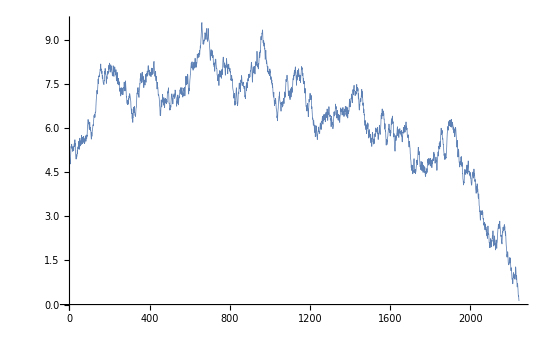

```mathematica
ListLinePlot[TestList1,ImageSize->550,PlotStyle->{Thickness[0.001]}]
```

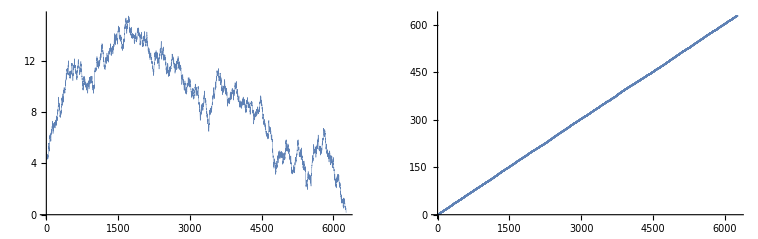

```mathematica
GraphicsRow[{ListLinePlot[TestList1,ImageSize->350,PlotStyle->{Thickness[0.001]}],
ListPlot[WalkDistances[TestList1],ImageSize->350]}]
```

```mathematica
TestList2=WalkUntilHitList[0.1,7,400,100,5];
```

```mathematica
TestList2d=WalkDistances[TestList2];
```

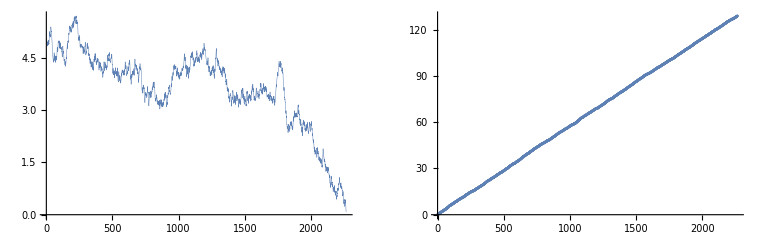

```mathematica
GraphicsRow[{ListLinePlot[TestList2,ImageSize->350,PlotStyle->{Thickness[0.001]}],
ListPlot[TestList2d,ImageSize->350]}]
```

```mathematica
TestList3=WalkUntilHitList[0.1,20,400,100,5];
```

```mathematica
TestList3d=WalkDistances[TestList3];
```

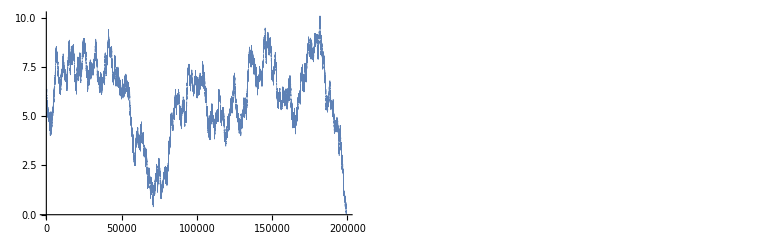

```mathematica
GraphicsRow[{ListLinePlot[TestList3,ImageSize->350,PlotStyle->{Thickness[0.001]}],
ListPlot[TestList3d,ImageSize->350]}]
```

```mathematica
TestList2=WalkUntilHitList[0.25,6,400,100,5];
```

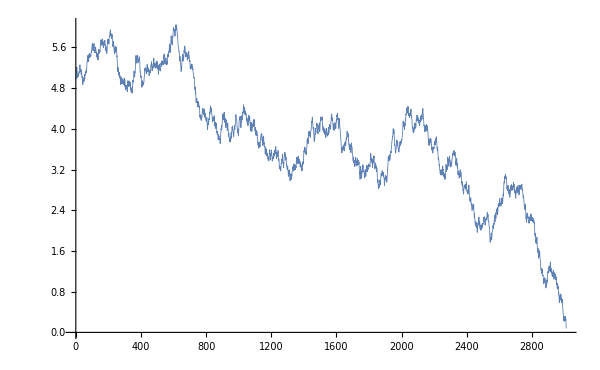

```mathematica
ListLinePlot[TestList2,ImageSize->600,PlotStyle->{Thickness[0.001]}]
```